# Information processing in EI networks

```mathematica
(* Assume that system is stable *)
$Assumptions = {r+kw>w, w>0, k>0,r>0,D>0, τ>0,i>0,j>0}
```

{kw+r>w,w>0,k>0,r>0,D>0,τ>0,i>0,j>0}

```mathematica
(*Interaction matrix*)
F = {{-r+w, -k w}, {w, -r-k w}};
(*Diffusion vector - scaled by factor 2*)
dM={{1/2,0},{0,1/2}};
```

## DERIVE MEAN & COVARIANCE MATRIX

### Time-varying mean

```mathematica
(*Define the system of differential equations*)
system={
τ x1'[t]==F[[1,1]]*x1[t]+F[[1,2]]*x2[t]+h,
τ x2'[t]==F[[2,1]]*x1[t]+F[[2,2]]*x2[t]+h
};
(*Define the initial condition*)
initialCondition={x1[0]==0,x2[0]==0};
(*Solve the system*)
solution=DSolve[Join[system,initialCondition],{x1[t],x2[t]},t];
meanTimeDep={x1[t]/.solution[[1,1]], x2[t]/.solution[[1,2]]}//FullSimplify
```

{((1-ⅇ^(-(t (r+(-1+k) w))/τ)) h)/(r+(-1+k) w),((1-ⅇ^(-(t (r+(-1+k) w))/τ)) h)/(r+(-1+k) w)}

```mathematica
simpleMeanTimeDep = meanTimeDep/.{r+w(k-1)->beta};
simpleMeanTimeDep = simpleMeanTimeDep/.{r+wk-w->beta};
simpleMeanTimeDep = simpleMeanTimeDep/.{w(k-1)-> wplus}
```

{(h ((-1+ⅇ^(-(beta t)/τ)+k-ⅇ^(-(r t)/τ) k) r+(1-ⅇ^(-(r t)/τ)) k wplus))/(beta (-1+k) r),(h (-beta ⅇ^(-(r t)/τ)+ⅇ^(-(beta t)/τ) r+wplus))/(beta (-1+k) r)}

```mathematica
(*Compute the limit for large time*)
meanSt = Limit[meanTimeDep,t->Infinity]
```

{ConditionalExpression[h/(r+(-1+k) w), h∈ℝ&&r+k w>w],ConditionalExpression[h/(r+(-1+k) w), h∈ℝ&&r+k w>w]}

{ConditionalExpression[h/(r+(-1+k) w), h∈ℝ&&r+k w>w],ConditionalExpression[h/(r+(-1+k) w), h∈ℝ&&r+k w>w]}

{ConditionalExpression[h/(r+(-1+k) w), h∈ℝ&&r+k w>w],ConditionalExpression[h/(r+(-1+k) w), h∈ℝ&&r+k w>w]}

{ConditionalExpression[(h (r+k w))/(r (r+(-1+k) w)), h∈ℝ&&k<1&&r+k w>w],ConditionalExpression[(h w)/(r (r+(-1+k) w)), h∈ℝ&&k<1&&r+k w>w]}

{ConditionalExpression[h/(r+(-1+k) w), h∈ℝ&&r+k w>w],ConditionalExpression[h/(r+(-1+k) w), h∈ℝ&&r+k w>w]}

{ConditionalExpression[(h (r+k w))/(r (r+(-1+k) w)), h∈ℝ&&k<1&&r+k w>w],ConditionalExpression[(h w)/(r (r+(-1+k) w)), h∈ℝ&&k<1&&r+k w>w]}

{ConditionalExpression[(h (r+k w))/(r (r+(-1+k) w)), h∈ℝ&&k<1&&r+k w>w],ConditionalExpression[(h w)/(r (r+(-1+k) w)), h∈ℝ&&k<1&&r+k w>w]}

{ConditionalExpression[(he (r+k w))/(r (r+(-1+k) w)), he∈ℝ&&k<1&&r+k w>w],ConditionalExpression[(he w)/(r (r+(-1+k) w)), he∈ℝ&&k<1&&r+k w>w]}

{ConditionalExpression[(he r+(he-hi) k w)/(r (r+(-1+k) w)), ],ConditionalExpression[(hi (r-w)+he w)/(r (r+(-1+k) w)), ]}

{ConditionalExpression[(h0 r+(h0-h1) k w)/(r (r+(-1+k) w)), ],ConditionalExpression[(h1 (r-w)+h0 w)/(r (r+(-1+k) w)), ]}

{ConditionalExpression[(h (r+k w))/(r (r+(-1+k) w)), h∈ℝ&&k<1&&r+k w>w],ConditionalExpression[(h w)/(r (r+(-1+k) w)), h∈ℝ&&k<1&&r+k w>w]}

{ConditionalExpression[h/(r+(-1+k) w), h∈ℝ&&r+k w>w],ConditionalExpression[h/(r+(-1+k) w), h∈ℝ&&r+k w>w]}

{ConditionalExpression[h/(r+(-1+k) w), h∈ℝ&&r+k w>w],ConditionalExpression[h/(r+(-1+k) w), h∈ℝ&&r+k w>w]}

{ConditionalExpression[h/(r+(-1+k) w), h∈ℝ&&r+k w>w],ConditionalExpression[h/(r+(-1+k) w), h∈ℝ&&r+k w>w]}

### Time-varying covariance matrix

```mathematica
(*Compute eigenvalues of - coupling matrix*)
Λ0=-F;
λ=Eigenvalues[Λ0]//FullSimplify
```

{1,1+(-1+k) w}

```mathematica
(*Compute eigenvectors*)
u1=Eigenvectors[Λ0][[1]]//FullSimplify;
v1=(Eigenvectors@Transpose[Λ0])[[1]]//FullSimplify;
u2=Eigenvectors[Λ0][[2]]//FullSimplify;
v2=(Eigenvectors@Transpose[Λ0])[[2]]//FullSimplify;
subABC=Flatten[Solve[Flatten[{Flatten[Table[Av v1[[i]] Au u1[[j]]+Bv v2[[i]] Bu u2[[j]]==If[i==j,1,0],{i,1,2},{j,1,2}]],
Av v1[[1]] Au u1[[1]]+Av v1[[2]] Au u1[[2]]==1,
Bv v2[[1]] Bu u2[[1]]+Bv v2[[2]] Bu u2[[2]]==1}]/.{Au->1,Bu->1},{Av,Bv}]//FullSimplify];
v1=Av v1/.subABC;
v2=Bv v2/.subABC;
(*Check that the coupling matrix is recovered*)
Table[λ[[1]] u1[[i]] v1[[j]]+λ[[2]] u2[[i]] v2[[j]],{i,1,2},{j,1,2}]//FullSimplify
```

{{1-w,k w},{-w,1+k w}}

```mathematica
(*Compute general solution*)
d11=Sum[v1[[i]] dM[[i,i]]v1[[i]],{i,1,2}];
d12=Sum[v1[[i]] dM[[i,i]]v2[[i]],{i,1,2}];
d21=Sum[v2[[i]] dM[[i,i]]v1[[i]],{i,1,2}];
d22=Sum[v2[[i]] dM[[i,i]]v2[[i]],{i,1,2}];
λ1=λ[[1]];
λ2=λ[[2]];
sigmaTimeDep=Table[2 (1-Exp[-λ1 t-λ1 t])/(λ1+λ1) d11 u1[[i]] u1[[j]]+2 (1-Exp[-λ1 t-λ2 t])/(λ1+λ2) d12 u1[[i]] u2[[j]]+2 (1-Exp[-λ2 t-λ1 t])/(λ2+λ1) d21 u2[[i]] u1[[j]]+2 (1-Exp[-λ2 t-λ2 t])/(λ2+λ2) d22 u2[[i]] u2[[j]],{i,1,2},{j,1,2}]//Simplify;
(*Impose that the off-diagonal have the same expression - already checked that they are equal*)
sigmaTimeDep[[2,1]] = sigmaTimeDep[[1,2]];
sigmaTimeDep
```

{{(ⅇ^(-2 t) (4 ⅇ^(-((-1+k) t w)) k (1+k) (1+(-1+k) w)-ⅇ^(-2 (-1+k) t w) (1+k^2) (2+(-1+k) w)-2 k^2 (2+3 (-1+k) w+(-1+k)^2 w^2)+ⅇ^(2 t) (-1+k)^2 (2+(-1+3 k) w+2 k^2 w^2)))/(2 (-1+k)^2 (1+(-1+k) w) (2+(-1+k) w)),(ⅇ^(-2 t) (2 ⅇ^(-((-1+k) t w)) (1+k)^2 (1+(-1+k) w)-ⅇ^(-2 (-1+k) t w) (1+k^2) (2+(-1+k) w)-2 k (2+3 (-1+k) w+(-1+k)^2 w^2)+ⅇ^(2 t) (-1+k)^2 w (1+k (-1+2 w))))/(2 (-1+k)^2 (1+(-1+k) w) (2+(-1+k) w))},{(ⅇ^(-2 t) (2 ⅇ^(-((-1+k) t w)) (1+k)^2 (1+(-1+k) w)-ⅇ^(-2 (-1+k) t w) (1+k^2) (2+(-1+k) w)-2 k (2+3 (-1+k) w+(-1+k)^2 w^2)+ⅇ^(2 t) (-1+k)^2 w (1+k (-1+2 w))))/(2 (-1+k)^2 (1+(-1+k) w) (2+(-1+k) w)),(ⅇ^(-2 t) (4 ⅇ^(-((-1+k) t w)) (1+k) (1+(-1+k) w)-ⅇ^(-2 (-1+k) t w) (1+k^2) (2+(-1+k) w)+ⅇ^(2 t) (-1+k)^2 (2+(-3+k) w+2 w^2)-2 (2+3 (-1+k) w+(-1+k)^2 w^2)))/(2 (-1+k)^2 (1+(-1+k) w) (2+(-1+k) w))}}

```mathematica
simpleSigmaTimeDep = sigmaTimeDep/.{1+w(k-1)->beta};
simpleSigmaTimeDep = simpleSigmaTimeDep/.{1+wk-w->beta};
simpleSigmaTimeDep = simpleSigmaTimeDep/.{w(k-1)-> wplus}
```

{{(ⅇ^(-2 t) (4 beta ⅇ^(-t wplus) k (1+k)+ⅇ^(2 t) (-1+k)^2 (2+(-1+3 k) w+2 k^2 w^2)-ⅇ^(-2 t wplus) (1+k^2) (2+wplus)-2 k^2 (2+(-1+k)^2 w^2+3 wplus)))/(2 beta (-1+k)^2 (2+wplus)),(ⅇ^(-2 t) (2 beta ⅇ^(-t wplus) (1+k)^2+ⅇ^(2 t) (-1+k)^2 w (1+k (-1+2 w))-ⅇ^(-2 t wplus) (1+k^2) (2+wplus)-2 k (2+(-1+k)^2 w^2+3 wplus)))/(2 beta (-1+k)^2 (2+wplus))},{(ⅇ^(-2 t) (2 beta ⅇ^(-t wplus) (1+k)^2+ⅇ^(2 t) (-1+k)^2 w (1+k (-1+2 w))-ⅇ^(-2 t wplus) (1+k^2) (2+wplus)-2 k (2+(-1+k)^2 w^2+3 wplus)))/(2 beta (-1+k)^2 (2+wplus)),(ⅇ^(-2 t) (4 beta ⅇ^(-t wplus) (1+k)+ⅇ^(2 t) (-1+k)^2 (2+(-3+k) w+2 w^2)-ⅇ^(-2 t wplus) (1+k^2) (2+wplus)-2 (2+(-1+k)^2 w^2+3 wplus)))/(2 beta (-1+k)^2 (2+wplus))}}

```mathematica
(*Check that initial condition is 0*)
sigmaTimeDep/.{t->0}//FullSimplify
```

{{0,0},{0,0}}

```mathematica
(*Check that stationary solution is equal to the solution of the Lyapunov equation*)
tmpSigmaSt=Limit[sigmaTimeDep,t->+Infinity]
```

{{(2+(-1+3 k) w+2 k^2 w^2)/(2 (1+(-1+k) w) (2+(-1+k) w)),(w (1+k (-1+2 w)))/(2 (1+(-1+k) w) (2+(-1+k) w))},{(w (1+k (-1+2 w)))/(2 (1+(-1+k) w) (2+(-1+k) w)),(2+(-3+k) w+2 w^2)/(2 (1+(-1+k) w) (2+(-1+k) w))}}

```mathematica
tt1[[2,2]]//TeXForm
```

Part::partd: Part specification tt1⟦2,2⟧ is longer than depth of object.

\text{tt1}[[2,2]]

### Stationary covariance matrix from Lyapunov equation

```mathematica
sigma = {{a, b}, {c,d}};
eye = {{1,0},{0,1}};
sol = Solve[{F.sigma + sigma.(Transpose[F])==-2D eye}, {a,b,c,d}][[1]];
sigmaSt= sigma /. sol;
sigmaSt =sigmaSt//FullSimplify;
sigmaSt // MatrixForm
```

((D (2 r^2+(-1+3 k) r w+2 k^2 w^2))/(r (r+(-1+k) w) (2 r+(-1+k) w)) | (D w (r-k r+2 k w))/(r (r+(-1+k) w) (2 r+(-1+k) w))
(D w (r-k r+2 k w))/(r (r+(-1+k) w) (2 r+(-1+k) w)) | (D (2 r^2+(-3+k) r w+2 w^2))/(r (r+(-1+k) w) (2 r+(-1+k) w)))

### Alternative solution

```mathematica
tt = tmpSigmaSt - MatrixExp[F*t].tmpSigmaSt.Transpose[ MatrixExp[F*t]];
tt//FullSimplify
```

{{(ⅇ^(-2 t) (4 ⅇ^(-((-1+k) t w)) k (1+k) (1+(-1+k) w)-ⅇ^(-2 (-1+k) t w) (1+k^2) (2+(-1+k) w)-2 k^2 (1+(-1+k) w) (2+(-1+k) w)+ⅇ^(2 t) (-1+k)^2 (2+w (-1+k (3+2 k w)))))/(2 (-1+k)^2 (1+(-1+k) w) (2+(-1+k) w)),(ⅇ^(-2 t) (-4 k+ⅇ^(-2 (-1+k) t w) (2 ⅇ^((-1+k) t w) (1+k)^2 (1+(-1+k) w)-(1+k^2) (2+(-1+k) w))+(-1+k) w (-6 k+(-1+k) (-2 k w+ⅇ^(2 t) (1+k (-1+2 w))))))/(2 (-1+k)^2 (1+(-1+k) w) (2+(-1+k) w))},{(ⅇ^(-2 t) (-4 k+ⅇ^(-2 (-1+k) t w) (2 ⅇ^((-1+k) t w) (1+k)^2 (1+(-1+k) w)-(1+k^2) (2+(-1+k) w))+(-1+k) w (-6 k+(-1+k) (-2 k w+ⅇ^(2 t) (1+k (-1+2 w))))))/(2 (-1+k)^2 (1+(-1+k) w) (2+(-1+k) w)),(ⅇ^(-2 t) (4 ⅇ^(-((-1+k) t w)) (1+k) (1+(-1+k) w)-ⅇ^(-2 (-1+k) t w) (1+k^2) (2+(-1+k) w)-2 (1+(-1+k) w) (2+(-1+k) w)+ⅇ^(2 t) (-1+k)^2 (2+w (-3+k+2 w))))/(2 (-1+k)^2 (1+(-1+k) w) (2+(-1+k) w))}}

```mathematica
(sigmaTimeDep-tt)//FullSimplify
```

{{0,0},{0,0}}

```mathematica
(-Inverse[F].{h0,0})//FullSimplify
```

{(h0+h0 k w)/(1+(-1+k) w),(h0 w)/(1+(-1+k) w)}

## MASTER EQUATION FOR THE INPUTS

### Uniform rates

```mathematica
M={{-4,a,a,a,a},{1,-a,0,0,0},{1,0,-a,0,0},{1,0,0,-a,0},{1,0,0,0,-a}};
```

```mathematica
M//MatrixForm
```

(-4 | a | a | a | a
1 | -a | 0 | 0 | 0
1 | 0 | -a | 0 | 0
1 | 0 | 0 | -a | 0
1 | 0 | 0 | 0 | -a)

```mathematica
Assuming[{a>0},Simplify[Eigensystem[M]]]
```

{{0,-4-a,-a,-a,-a},{{a,1,1,1,1},{-4,1,1,1,1},{0,-1,0,0,1},{0,-1,0,1,0},{0,-1,1,0,0}}}

### Exponential rates

```mathematica
K = 4;
M={{-Total[Table[Exp[-beta k delta],{k,K}]],1,1,1,1},{Exp[-beta delta],-1,0,0,0},{Exp[-beta 2 delta],0,-1,0,0},{Exp[-beta 3 delta],0,0,-1,0},{Exp[-beta 4 delta],0,0,0,-1}};
M//MatrixForm
```

(-ⅇ^(-4 beta delta)-ⅇ^(-3 beta delta)-ⅇ^(-2 beta delta)-ⅇ^(-beta delta) | 1 | 1 | 1 | 1
ⅇ^(-beta delta) | -1 | 0 | 0 | 0
ⅇ^(-2 beta delta) | 0 | -1 | 0 | 0
ⅇ^(-3 beta delta) | 0 | 0 | -1 | 0
ⅇ^(-4 beta delta) | 0 | 0 | 0 | -1)

```mathematica
Assuming[{beta>0 && delta > 0},Simplify[Eigensystem[M]]]
```

{{0,-1,-1,-1,-ⅇ^(-4 beta delta) (1+ⅇ^(beta delta)+ⅇ^(2 beta delta)+ⅇ^(3 beta delta)+ⅇ^(4 beta delta))},{{ⅇ^(4 beta delta),ⅇ^(3 beta delta),ⅇ^(2 beta delta),ⅇ^(beta delta),1},{0,-1,0,0,1},{0,-1,0,1,0},{0,-1,1,0,0},{-1-ⅇ^(beta delta)-ⅇ^(2 beta delta)-ⅇ^(3 beta delta),ⅇ^(3 beta delta),ⅇ^(2 beta delta),ⅇ^(beta delta),1}}}

## COMPUTE CHERNOFF AND KL DIVERGENCE

Define network variables

```mathematica
xe[h_] := Evaluate[meanSt[[1]]]
xi[h_]:= Evaluate[meanSt[[2]]]
x[h_]:= {xe[h],xi[h]};

(*
xe[hx_,hy_] := Evaluate[meanSt[[1]]]
xi[hx_,hy_]:= Evaluate[meanSt[[2]]]
x[hx_,hy_]:= {xe[hx,hy],xi[hx,hy]};
*)
```

Define pairwise distances

```mathematica
ch[x1_,x2_]:=1/8 Transpose[x1-x2].Inverse[sigmaSt].(x1-x2);
kl[x1_,x2_]:=1/2 Transpose[x1-x2].Inverse[sigmaSt].(x1-x2);
```

```mathematica
Simplify[ kl[x[i dh],x[j dh]] ]
```

ConditionalExpression[(dh^2 (i-j)^2 (2 r+(-1+k) w)^2)/(2 D (r+(-1+k) w) (2 r^2+2 (-1+k) r w+(1+k^2) w^2)), dh∈ℝ&&r+k w>w]

```mathematica
Simplify[ ch[x[i dh],x[j dh]] ]
```

ConditionalExpression[(dh^2 (i-j)^2 (2 r+(-1+k) w)^2)/(8 D (r+(-1+k) w) (2 r^2+2 (-1+k) r w+(1+k^2) w^2)), dh∈ℝ&&r+k w>w]

```mathematica
etaGlobal=(2 r+(-1+k) w)^2/(2 (r+(-1+k) w) (2 r^2+2 (-1+k) r w+(1+k^2) w^2));
etaLocal=((2 r+(-1+k) w) (2 r^2+(-1+3 k) r w+(1+k^2) w^2))/(4 r (r+(-1+k) w) (2 r^2+2 (-1+k) r w+(1+k^2) w^2));
```

```mathematica
ratio=etaGlobal/etaLocal//FullSimplify
```

(2 r (2 r+(-1+k) w))/(2 r^2+(-1+3 k) r w+(1+k^2) w^2)

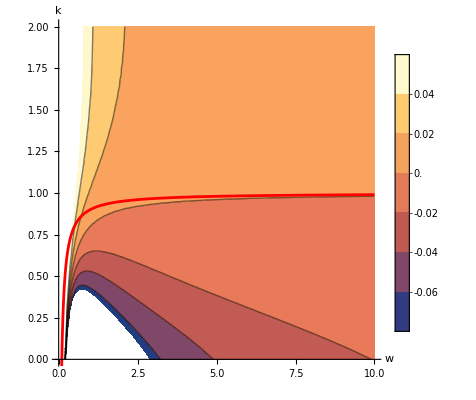

```mathematica
Show[ContourPlot[(2 r (2 r+(-1+k) w))/(2 r^2+(-1+3 k) r w+(1+k^2) w^2)/. {r->0.1},{w,0,10},{k,0,2},PlotLegends->Automatic,AxesLabel->Automatic,Frame->False,Axes->True],ParametricPlot[{w,(1-r/w)/.{r->0.1}},{w,0,10},PlotStyle->{Red,Thick}]]
```

```mathematica
Reduce[{(2 r (2 r+(-1+k) w))/(2 r^2+(-1+3 k) r w+(1+k^2) w^2)>=1,k w+r>w,w>0,k>0,r>0},{k,w,r},Reals]//FullSimplify
```

4 r≥(1+k+√(9+k (2+9 k))) w

```mathematica
Reduce[{(2 (2+(-1+k) w))/(2+(-1+3 k) w+(1+k^2) w^2)>=1k w+1>w,w>0,k>0},{w,k},Reals]//FullSimplify
```

w<1&&k≤Root[-2+w+w^2+(3 w-w^2+w^3) #1+4 w^2 #1^2+w^3 #1^3&,3]

Define input variables

```mathematica
M = 3;
K = M-1;
pi = Join[{wdown},ConstantArray[wup, K]];
pi = pi / (wdown + K wup);
```

```mathematica
Ilow[dh_]:=-Simplify[ Total[ Table[ pi[[i]] Log[ Total[ Table[pi[[j]]Exp[-ch[x[i dh],x[j dh]]],{j,M}]]], {i,M}]]]
Ihigh[dh_]:=-Simplify[ Total[ Table[ pi[[i]]Log[Total[ Table[pi[[j]]Exp[-kl[x[i dh],x[j dh]]],{j,M}]]], {i,M}] ]]
```

```mathematica
(*Ilow[dh]/.{(dh^2 (2 r+(-1+k) w) (2 r^2+(-1+3 k) r w+(1+k^2) w^2))/(D r (r+(-1+k) w) (2 r^2+2 (-1+k) r w+(1+k^2) w^2))->W}
Ihigh[dh]/.{(dh^2 (2r+(-1+k) w) (2 r^2+(-1+3 k) r w+(1+k^2) w^2))/(D  r(r+(-1+k) w) (2 r^2+2 (-1+k)r w+(1+k^2) w^2))->W}*)
Ilow[dh]/.{(dh^2 (2 r+(-1+k) w)^2)/(D (r+(-1+k) w) (2 r^2+2 (-1+k) r w+(1+k^2) w^2))->W}
Ihigh[dh]/.{(dh^2 (2 r+(-1+k) w)^2)/(D (r+(-1+k) w) (2 r^2+2 (-1+k) r w+(1+k^2) w^2))->W}
```

ConditionalExpression[-(wup Log[(ⅇ^(-W/2) wdown+wup+ⅇ^(-W/8) wup)/(wdown+2 wup)]+wup Log[(ⅇ^(-W/8) (wdown+wup+ⅇ^(W/8) wup))/(wdown+2 wup)]+wdown Log[(wdown+ⅇ^(-W/2) (1+ⅇ^(3 W/8)) wup)/(wdown+2 wup)])/(wdown+2 wup), dh∈ℝ&&r+k w>w]

ConditionalExpression[-(wup Log[(ⅇ^(-2 W) wdown+wup+ⅇ^(-W/2) wup)/(wdown+2 wup)]+wup Log[(ⅇ^(-W/2) (wdown+wup+ⅇ^(W/2) wup))/(wdown+2 wup)]+wdown Log[(wdown+ⅇ^(-2 W) (1+ⅇ^(3 W/2)) wup)/(wdown+2 wup)])/(wdown+2 wup), dh∈ℝ&&r+k w>w]

```mathematica
Ilow[0]
Ihigh[0]
```

ConditionalExpression[0, r+k w>w]

ConditionalExpression[0, r+k w>w]

```mathematica
Limit[Ilow[dh], dh->Infinity]
```

ConditionalExpression[-(wdown Log[wdown/(wdown+2 wup)]+2 wup Log[wup/(wdown+2 wup)])/(wdown+2 wup), r+k w>w]

```mathematica
(*Wr[k_,w_,r_]:=((2 r+(-1+k) w) (2 r^2+(-1+3 k) r w+(1+k^2) w^2))/(r (r+(-1+k) w) (2 r^2+2 (-1+k) r w+(1+k^2) w^2))*)
Wr[k_,w_,r_]:=(2 r+(-1+k) w)^2/((r+(-1+k) w) (2 r^2+2 (-1+k) r w+(1+k^2) w^2))
```

```mathematica
W[k_,w_]:=Wr[k,w,1]
```

```mathematica
W[k,w]
```

(2+(-1+k) w)^2/((1+(-1+k) w) (2+2 (-1+k) w+(1+k^2) w^2))

```mathematica
Limit[W[k,w],{k->1-1/w}]
```

Limit::alimv: Warning: Assumptions that involve the limit variable are ignored.

Indeterminate

```mathematica
Solve[W[k,w]==1.5,{k,w}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Solve::svars: Equations may not give solutions for all "solve" variables.

{{k→ConditionalExpression[Root[-2.-4. w+3. w^2-1. w^3+(-4. w-4. w^2+w^3) #1+(-1. w^2-1. w^3) #1^2+w^3 #1^3&,1], 0.0564512<w<1.||w>1.]},{k→ConditionalExpression[Root[-2.-4. w+3. w^2-1. w^3+(-4. w-4. w^2+w^3) #1+(-1. w^2-1. w^3) #1^2+w^3 #1^3&,3], 0<w≤0.0564512]},{k→4.,w→1.}}

Power::infy: Infinite expression 1/0. encountered.

Greater::nord: Invalid comparison with ComplexInfinity attempted.

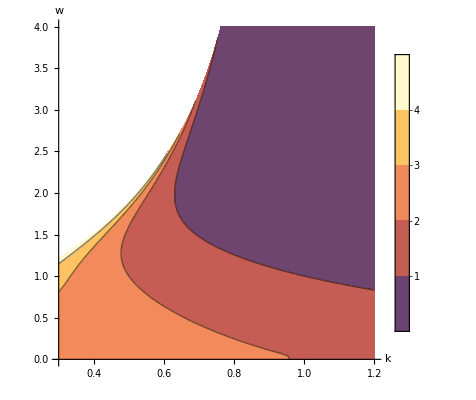

```mathematica
ContourPlot[W[k,w],{k,0.3,1.2},{w,0,4},PlotLegends->Automatic, AxesLabel->Automatic,Frame->False,Axes->True,RegionFunction->Function[{k,w,z},z>0]]
```

## Time-varying mutual information

```mathematica
(*Define params of dynamics*)
K={{kx,k01},{ky,k11}};
h={h0,0};
x={xE, xI};
sigma = {{σE^2,ρ},{ρ,σI^2}};

(*Define propagator*)
pdf = MultinormalDistribution[h,sigma];
pdf = PDF[pdf,x]//Simplify
```

(ⅇ^((2 h0 xI ρ-2 xE xI ρ+xI^2 σE^2+h0^2 σI^2-2 h0 xE σI^2+xE^2 σI^2)/(2 ρ^2-2 σE^2 σI^2)))/(2 π √(-ρ^2+σE^2 σI^2))

### Normally distributed input

```mathematica
$Assumptions = {kx>0, ky>0,h0>0, xE>0, xI>0,Det[sigma]>0,ρ>0;σE>0;σI>0; λ>0;σh>0 };
```

```mathematica
ph=NormalDistribution[λ,σh];
ph=PDF[ph,h0];
```

```mathematica
px = Integrate[pdf*ph,{h0,-Infinity,Infinity}];
```

```mathematica
px
```

(ⅇ^((xI (-2 xE ρ+2 λ ρ+xI (σE^2+σh^2))+(xE-λ)^2 σI^2)/(2 ρ^2-2 (σE^2+σh^2) σI^2)))/(2 π √(-ρ^2+(σE^2+σh^2) σI^2))

```mathematica
muE = Integrate[xE*px,{xE,-Infinity,+Infinity},{xI,-Infinity,+Infinity}];
muI =Integrate[xI*px,{xE,-Infinity,+Infinity},{xI,-Infinity,+Infinity}];
varE = Integrate[xE^2*px,{xE,-Infinity,+Infinity},{xI,-Infinity,+Infinity}];
varI = Integrate[xI^2*px,{xE,-Infinity,+Infinity},{xI,-Infinity,+Infinity}];
varE = varE-muE^2;
varI = varI-muI^2;
cov = Integrate[(xE-muE)*(xI-muI)*px,{xE,-Infinity,+Infinity},{xI,-Infinity,+Infinity}];
```

```mathematica
muE
muI
varE
varI
cov
```

λ

0

σE^2+σh^2

σI^2

ρ

```mathematica
ttt = MultinormalDistribution[{muE, muI},{{varE, cov},{cov, varI}}];
PDF[ttt,{xE,xI}]//FullSimplify
```

(ⅇ^((xI (-2 xE ρ+2 λ ρ+xI (σE^2+σh^2))+(xE-λ)^2 σI^2)/(2 ρ^2-2 (σE^2+σh^2) σI^2)))/(2 π √(-ρ^2+(σE^2+σh^2) σI^2))

### Exponentially distributed input

```mathematica
$Assumptions = {kx>0, ky>0,h0>0, xE>0, xI>0,Det[sigma]>0,ρ>0;σE>0;σI>0; λ>0;σh>0 };
```

```mathematica
ph=λ Exp[-λ h0];
ph=NormalDistribution[λ,σh];
ph=PDF[ph,h0];
```

```mathematica
Integrate[ph,{h0,-Infinity,Infinity}]
```

1

```mathematica
int = Integrate[pdf*ph,{h0,-Infinity,Infinity}];
```

```mathematica
i = Integrate[pdf*ph,{h0,-Infinity,Infinity}];
```

```mathematica
int
```

(ⅇ^((xI (-2 xE ρ+2 λ ρ+xI (σE^2+σh^2))+(xE-λ)^2 σI^2)/(2 ρ^2-2 (σE^2+σh^2) σI^2)))/(2 π √(-ρ^2+(σE^2+σh^2) σI^2))

```mathematica
logterm = Log[int]//FullSimplify
```

1/2 (-2 xE λ+λ^2 σE^2-(xI-λ ρ)^2/σI^2-Log[8 π]+2 Log[(λ (1+Erf[(-xI ρ+λ ρ^2+(xE-λ σE^2) σI^2)/(√(-2 ρ^2 σI^2+2 σE^2 σI^4))]))/Abs[σI]])

```mathematica
integrand =logterm*int//FullSimplify
```

(ⅇ^(1/2 (-2 xE λ+λ^2 σE^2-(xI-λ ρ)^2/σI^2)) λ (1+Erf[(-xI ρ+λ ρ^2+(xE-λ σE^2) σI^2)/(√(-2 ρ^2 σI^2+2 σE^2 σI^4))]) (-2 xE λ+λ^2 σE^2-(xI-λ ρ)^2/σI^2-Log[8 π]+2 Log[(λ (1+Erf[(-xI ρ+λ ρ^2+(xE-λ σE^2) σI^2)/(√(-2 ρ^2 σI^2+2 σE^2 σI^4))]))/Abs[σI]]))/(4 √(2 π) Abs[σI])

```mathematica
entropy=Integrate[integrand,{xE,-Infinity,Infinity},{xI,-Infinity,Infinity}]
```

Integrate::ilim: Invalid integration variable or limit(s) in {{xE,-∞,∞},{xI,-∞,∞}}.

Integrate[(ⅇ^(1/2 (-2 xE λ+λ^2 σE^2-(xI-λ ρ)^2/σI^2)) λ (1+Erf[(-xI ρ+λ ρ^2+(xE-λ σE^2) σI^2)/(√(-2 ρ^2 σI^2+2 σE^2 σI^4))]) (-2 xE λ+λ^2 σE^2-(xI-λ ρ)^2/σI^2-Log[8 π]+2 Log[(λ (1+Erf[(-xI ρ+λ ρ^2+(xE-λ σE^2) σI^2)/(√(-2 ρ^2 σI^2+2 σE^2 σI^4))]))/Abs[σI]]))/(4 √(2 π) Abs[σI]),{{xE,-∞,∞},{xI,-∞,∞}}]

### Uniformly distributed input

```mathematica
int = Integrate[pdf,{h0,0,hmax}];
```

```mathematica
int//Simplify
```

(ⅇ^(-xI^2/(2 σI^2)) √(ρ^2-σE^2 σI^2) (Erfi[(xI ρ+(hmax-xE) σI^2)/(√2 σI √(ρ^2-σE^2 σI^2))]-Erfi[(xI ρ-xE σI^2)/(√2 σI √(ρ^2-σE^2 σI^2))]))/(2 √(2 π) σI √(-ρ^2+σE^2 σI^2))

```mathematica
$Assumptions = {kx>0, ky>0,h0>0, xE>0, xI>0,Det[sigma]>0,ρ>0;σE>0;σI>0};
```

```mathematica
int//FullSimplify
```

(ⅈ ⅇ^(-xI^2/(2 σI^2)) (Erfi[(xI ρ+(hmax-xE) σI^2)/(√2 σI √((ρ-σE σI) (ρ+σE σI)))]-Erfi[(xI ρ-xE σI^2)/(√2 σI √((ρ-σE σI) (ρ+σE σI)))]))/(2 √(2 π) σI)

```mathematica
Inverse[sigma]
```

{{σI/(-ρ^2+σE σI),-ρ/(-ρ^2+σE σI)},{-ρ/(-ρ^2+σE σI),σE/(-ρ^2+σE σI)}}

```mathematica
Det[sigma]
```

-ρ^2+σE σI

```mathematica
sigma
```

{{σE^2,ρ},{ρ,σI^2}}

```mathematica
Integrate[Erf[x]*log[Erf[x]],{x,-Infinity,Infinity}]//Simplify
```

∫_(-∞)^∞ Erf[x] log[Erf[x]]ⅆx

## Analytical time-varying mutual information

```mathematica
Λ = MatrixExp[F*t];
K =-(IdentityMatrix[2]-Λ).Inverse[F]//FullSimplify;
Σh = {{σh^2,0},{0,σh^2}};
```

```mathematica
Λ/.{r->1}
```

{{-ⅇ^(t (-1+w-k w))/(-1+k)+(ⅇ^-t k)/(-1+k),-(ⅇ^-t k)/(-1+k)+(ⅇ^(t (-1+w-k w)) k)/(-1+k)},{ⅇ^-t/(-1+k)-ⅇ^(t (-1+w-k w))/(-1+k),-ⅇ^-t/(-1+k)+(ⅇ^(t (-1+w-k w)) k)/(-1+k)}}

```mathematica
Limit[K,t->Infinity]
```

{{ConditionalExpression[(r+k w)/(r (r+(-1+k) w)), k<1&&r+k w>w],ConditionalExpression[-(k w)/(r (r+(-1+k) w)), k<1&&r+k w>w]},{ConditionalExpression[w/(r (r+(-1+k) w)), k<1&&r+k w>w],ConditionalExpression[(r-w)/(r (r+(-1+k) w)), k<1&&r+k w>w]}}

```mathematica
KlimStable={{((-1+k) (1+k w))/(-1+k+(-1+k)^2 w),-(k (-1+k) w)/(-1+k+(-1+k)^2 w)},{((-1+k) w)/(-1+k+(-1+k)^2 w),(-(-1+k) (-1+w))/(-1+k+(-1+k)^2 w)}}//FullSimplify;
KlimEdge={{(1+(-1+k) (1+k w))/(-1+k+(-1+k)^2 w),-(k+k (-1+k) w)/(-1+k+(-1+k)^2 w)},{(1+(-1+k) w)/(-1+k+(-1+k)^2 w),(-k-(-1+k) (-1+w))/(-1+k+(-1+k)^2 w)}}//FullSimplify;
```

```mathematica
up = sigmaSt + K.Σh.Transpose[K]//FullSimplify;
upStable= sigmaSt + KlimStable.Σh.Transpose[KlimStable]//FullSimplify;
upUnstable= sigmaSt + KlimEdge.Σh.Transpose[KlimEdge]//FullSimplify;
down = sigmaSt;
```

```mathematica
detUp=Det[up]//FullSimplify;
detDown=Det[down]//FullSimplify;
```

```mathematica
mutual=0.5*Log[detUp/detDown]//FullSimplify;
mutualLimStable=0.5*Log[Det[upStable]/Det[down]]//FullSimplify;
mutualLimUnstable=0.5*Log[Det[upUnstable]/Det[down]]//FullSimplify;
```

```mathematica
mutual
```

0.5 Log[(ⅇ^(-2 (t+k t w)) (-4 ⅇ^((1+k) t w) (1+k) (1+(-1+k) w) (2+(-1+k) w) σh^2+2 ⅇ^(2 t w) (2+(-1+k) w)^2 σh^2+ⅇ^(2 k t w) (1+k^2) (1+(-1+k) w) (2+(-1+k) w)^2 σh^2+4 ⅇ^(t (1+w+k w)) (-1+k) (2+(-1+k) w) (1+k w) σh^2-2 ⅇ^(t+2 k t w) (-1+k) (1+(-1+k) w) (2+(-1+k) w) (w+k (2+k w)) σh^2+ⅇ^(2 (t+k t w)) (-1+k)^2 (2+4 σh^2+(-1+k) (1+k^2) w^3 (1+σh^2)+4 w (-1+k+(-1+2 k) σh^2)+w^2 (3-4 k+3 k^2+(3+k (-4+5 k)) σh^2))))/((-1+k)^2 (1+(-1+k) w) (2+w (-2+w+k (2+k w))))]

```mathematica
FortranForm[mutual]
```

0.5*Log((-4*E**((1 + k)*t*w)*(1 + k)*(1 + (-1 + k)*w)*(2 + (-1 + k)*w)*σh**2 + 
     -      2*E**(2*t*w)*(2 + (-1 + k)*w)**2*σh**2 + 
     -      E**(2*k*t*w)*(1 + k**2)*(1 + (-1 + k)*w)*(2 + (-1 + k)*w)**2*σh**2 + 
     -      4*E**(t*(1 + w + k*w))*(-1 + k)*(2 + (-1 + k)*w)*(1 + k*w)*σh**2 - 
     -      2*E**(t + 2*k*t*w)*(-1 + k)*(1 + (-1 + k)*w)*(2 + (-1 + k)*w)*(w + k*(2 + k*w))*σh**2 + 
     -      E**(2*(t + k*t*w))*(-1 + k)**2*(2 + 4*σh**2 + (-1 + k)*(1 + k**2)*w**3*(1 + σh**2) + 
     -         4*w*(-1 + k + (-1 + 2*k)*σh**2) + w**2*(3 - 4*k + 3*k**2 + (3 + k*(-4 + 5*k))*σh**2)))/
     -    (E**(2*(t + k*t*w))*(-1 + k)**2*(1 + (-1 + k)*w)*(2 + w*(-2 + w + k*(2 + k*w)))))

```mathematica
mutual/.{σh->1}
```

0.5 Log[(ⅇ^(-2 (t+k t w)) (-4 ⅇ^((1+k) t w) (1+k) (1+(-1+k) w) (2+(-1+k) w)+2 ⅇ^(2 t w) (2+(-1+k) w)^2+ⅇ^(2 k t w) (1+k^2) (1+(-1+k) w) (2+(-1+k) w)^2+4 ⅇ^(t (1+w+k w)) (-1+k) (2+(-1+k) w) (1+k w)+ⅇ^(2 (t+k t w)) (-1+k)^2 (6+4 (-2+3 k) w+(6+k (-8+8 k)) w^2+2 (-1+k) (1+k^2) w^3)-2 ⅇ^(t+2 k t w) (-1+k) (1+(-1+k) w) (2+(-1+k) w) (w+k (2+k w))))/((-1+k)^2 (1+(-1+k) w) (2+w (-2+w+k (2+k w))))]

```mathematica
mutualSt=Limit[mutual,t->Infinity]//FullSimplify
```

0.5 (-Log[(1+(-1+k) w) (2+w (-2+w+k (2+k w)))]+Log[2+4 σh^2+(-1+k) (1+k^2) w^3 (1+σh^2)+4 w (-1+k+(-1+2 k) σh^2)+w^2 (3-4 k+3 k^2+(3+k (-4+5 k)) σh^2)])

```mathematica
mutualDer=D[mutual,{t,2}];
```

```mathematica
limitDer=Limit[mutualDer,t->0]//FullSimplify
```

((4.+w (-8.+1. k^2 w+(7.-2. w) w+k (4.+w (-4.+2. w)))) σh^2)/(2.+w (-2.+w+k (2.+k w)))

```mathematica
zzz=(mutualSt limitDer)//FullSimplify
```

1/(2.+w (-2.+w+k (2.+k w)))0.5 (4.+w (-8.+1. k^2 w+(7.-2. w) w+k (4.+w (-4.+2. w)))) σh^2 (-Log[(1+(-1+k) w) (2+w (-2+w+k (2+k w)))]+Log[2+4 σh^2+(-1+k) (1+k^2) w^3 (1+σh^2)+4 w (-1+k+(-1+2 k) σh^2)+w^2 (3-4 k+3 k^2+(3+k (-4+5 k)) σh^2)])

```mathematica
FortranForm[zzz]
```

(0.5*(4. + w*(-8. + 1.*k**2*w + (7. - 2.*w)*w + k*(4. + w*(-4. + 2.*w))))*σh**2*
     -    (-Log((1 + (-1 + k)*w)*(2 + w*(-2 + w + k*(2 + k*w)))) + 
     -      Log(2 + 4*σh**2 + (-1 + k)*(1 + k**2)*w**3*(1 + σh**2) + 4*w*(-1 + k + (-1 + 2*k)*σh**2) + 
     -        w**2*(3 - 4*k + 3*k**2 + (3 + k*(-4 + 5*k))*σh**2))))/(2. + w*(-2. + w + k*(2. + k*w)))

```mathematica
Limit[limitDer,k->Infinity]
```

Limit::alimv: Warning: Assumptions that involve the limit variable are ignored.

1. σh

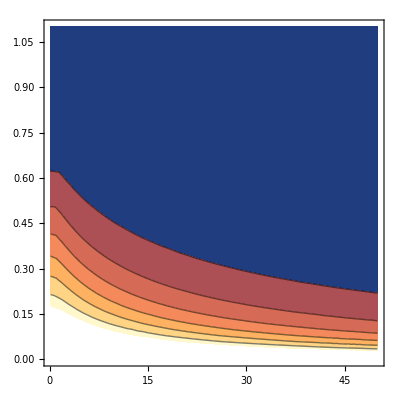

```mathematica
ContourPlot[limitDer/.{σh->1},{k,0.1,50},{w,0,1.10}]
```

```mathematica
mutualSt=Limit[mutual,t->Infinity]
```

0.5 Log[(2+4 σh+(-1+k-k^2+k^3) w^3 (1+σh)+4 w (-1+k-σh+2 k σh)+w^2 (3 (1+σh)-4 k (1+σh)+k^2 (3+5 σh)))/((1+(-1+k) w) (2+2 (-1+k) w+(1+k^2) w^2))]

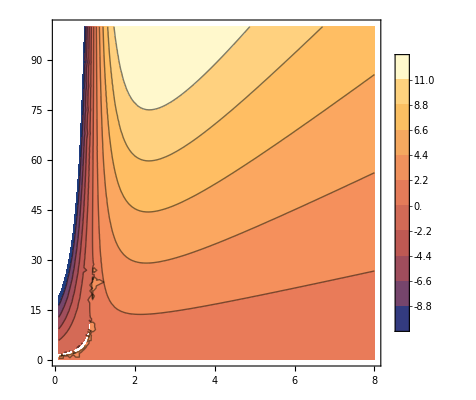

```mathematica
ContourPlot[(zzz)/.σh->1,{k,0.1,8},{w,0.1,100},PlotLegends->Automatic,Contours->10]
```

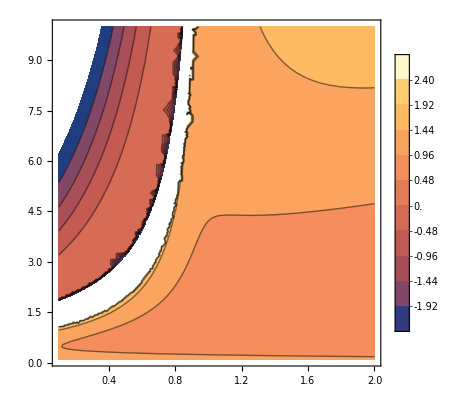

```mathematica
ContourPlot[(zzz)/.σh->1,{k,0.1,2},{w,0.1,10},PlotLegends->Automatic,Contours->10]
```

```mathematica
Limit[mutualSt,{k->1-1/w}]
```

Limit::alimv: Warning: Assumptions that involve the limit variable are ignored.

∞

```mathematica
zzz=((2+4 σh+(-1+k-k^2+k^3) w^3 (1+σh)+4 w (-1+k-σh+2 k σh)+w^2 (3 (1+σh)-4 k (1+σh)+k^2 (3+5 σh)))/((1+(-1+k) w) (2+2 (-1+k) w+(1+k^2) w^2))-1)/limitDer//FullSimplify
```

(4.+w (-4.+8. k+(3.+k (-4.+5. k)) w+1. (-1.+1. k) (1.+1. k^2) w^2))/((1.+(-1.+k) w) (4.+w (-8.+1. k^2 w+(7.-2. w) w+k (4.+w (-4.+2. w)))))

```mathematica
Limit[zzz,k->Infinity]
```

Limit::alimv: Warning: Assumptions that involve the limit variable are ignored.

1.

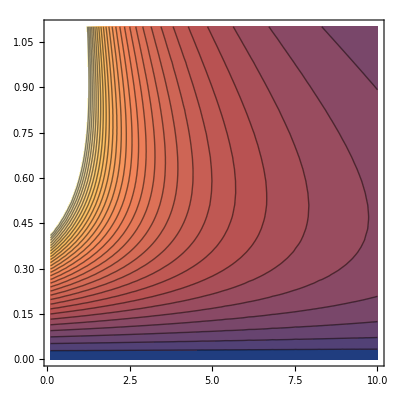

```mathematica
ContourPlot[zzz,{k,0.1,10},{w,0.,1.10},Contours->30]
```

```mathematica
mutualStFixed[k_,w_,σh_]:=Evaluate[mutualSt];
```

```mathematica
mutualStFixed[k,w,1]
```

0.5 Log[(6+4 (-2+3 k) w+(6-8 k+8 k^2) w^2+2 (-1+k-k^2+k^3) w^3)/((1+(-1+k) w) (2+2 (-1+k) w+(1+k^2) w^2))]

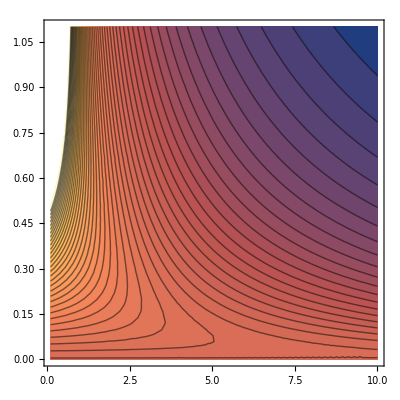

```mathematica
ContourPlot[mutualStFixed[k,w,1],{k,0.1,10},{w,0.,1.10},Contours->50]
```

```mathematica
Limit[mutual,k->1]
```

Limit::alimv: Warning: Assumptions that involve the limit variable are ignored.

0.5 Log[(1+2 σh+2 w σh-4 ⅇ^-t (1+(1+t) w+(1+t) w^2) σh+2 ⅇ^(-2 t) (1+w+2 t w+(1+2 t+2 t^2) w^2) σh+w^2 (1+2 σh))/(1+w^2)]

```mathematica
MutualTimeDep[t_,k_,w_,σh_]:=Evaluate[mutual];
```

```mathematica
MutualTimeDepFixed[t_,w_]:=MutualTimeDep[t,1.001,w,1];
```

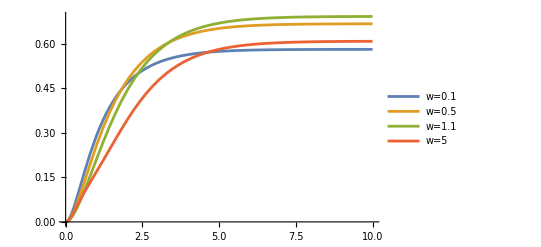

```mathematica
Plot[{MutualTimeDepFixed[t,0.1],MutualTimeDepFixed[t,0.5],MutualTimeDepFixed[t,1.1],MutualTimeDepFixed[t,5]},{t,0,10},PlotLegends->{"w=0.1","w=0.5","w=1.1","w=5"}]
```

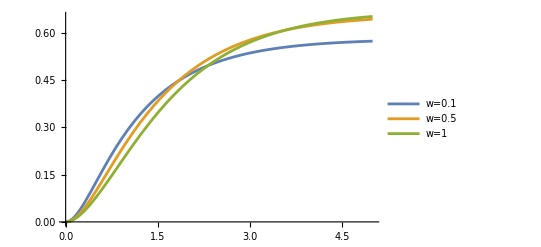

```mathematica
Plot[{MutualTimeDepFixed[t,0.1],MutualTimeDepFixed[t,0.5],MutualTimeDepFixed[t,1]},{t,0,5},PlotLegends->{"w=0.1","w=0.5","w=1"}]
```

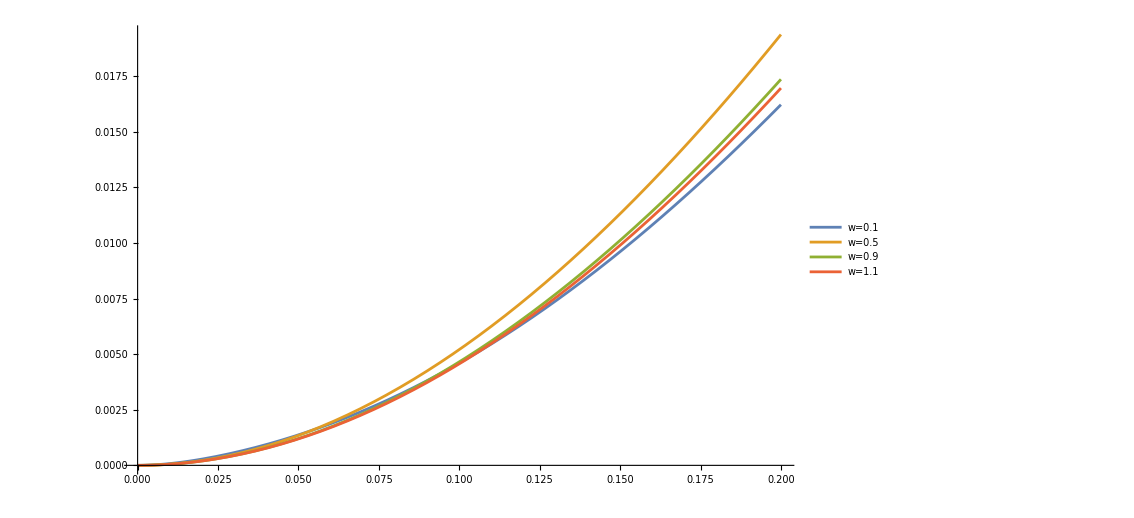

```mathematica
Plot[{MutualTimeDepFixed[t,5],MutualTimeDepFixed[t,0.5],MutualTimeDepFixed[t,0.9],MutualTimeDepFixed[t,1.1]},{t,0,0.2},PlotLegends->{"w=0.1","w=0.5","w=0.9","w=1.1"}]
```

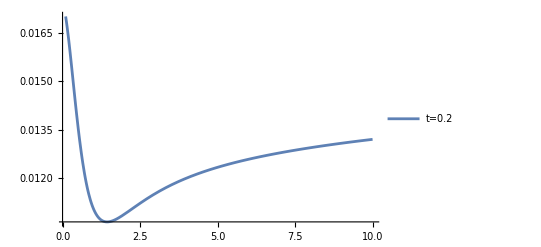

```mathematica
Plot[{MutualTimeDepFixed[0.2,w]*MutualTimeDepFixed[10,w]},{w,0.1,10},PlotLegends->{"t=0.2","t=10"}]
```

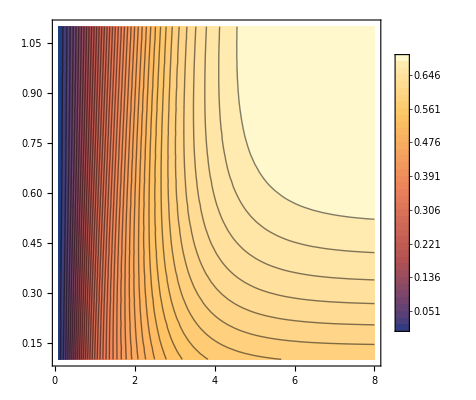

```mathematica
ContourPlot[MutualTimeDepFixed[t,w],{t,0.1,8},{w,0.1,1.10},PlotLegends->Automatic,Contours->40]
```

```mathematica
1/(0.9)
```

1.11111